Solving nonlinear differential equations with differentiable quantum circuits

Original authors of paper: Oleksandr Kyriienko, Annie E. Paine, and Vincent E. Elfving
Phys. Rev. A 103, 052416 (2021)
Notebook: Óscar Amaro, September 2023

## Figure 1

```mathematica
(* since the target function is even, the Chebyshev approximation should also have this symmetry*)
ChebyshevApprox[n_Integer?Positive,f_Function,x_]:=Module[{c,xk},xk=Pi (Range[n]-1/2)/n;
c[j_]=2*Total[Cos[j*xk]*(f/@Cos[xk])]/n;
Total[Table[c[k]*ChebyshevT[k,x],{k,0,n-1}]]-c[0]/2];
f=Exp[-1/(25#^2)]Cos[20 #]&
```

Exp[-1/(25 #1^2)] Cos[20 #1]&

```mathematica
Clear[x]
f2=ChebyshevApprox[2,f,x]//N;
f16=ChebyshevApprox[16,f,x]//N;
f64=ChebyshevApprox[64,f,x]//N//Simplify;(* some numerical instability, works better but slower if Simplify is applied before N *)
```

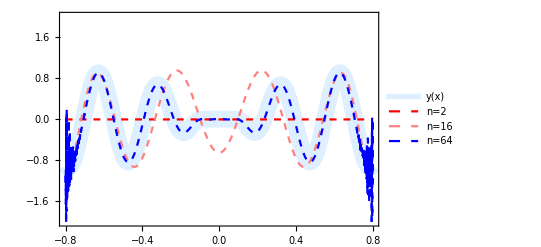

```mathematica
Plot[{f[x],f2,f16,f64},{x,-0.8,0.8},Frame->True,Axes->False,PlotRange->{-2,2},PlotLegends->{"y(x)","n=2","n=16","n=64"}, PlotStyle->{{LightBlue,Thickness[0.03]},{Dashed,Red},{Dashed,Pink},{Dashed,Blue}}]
```